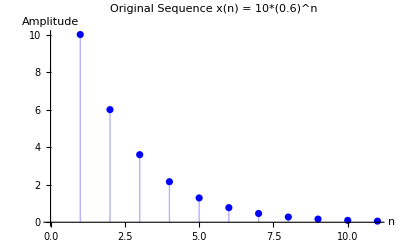

```mathematica
ListPlot[Table[10*(0.6)^n,{n,0,10}],Filling->Axis,PlotStyle->Blue,AxesLabel->{"n","Amplitude"},PlotLabel->"Original Sequence x(n) = 10*(0.6)^n"]
```

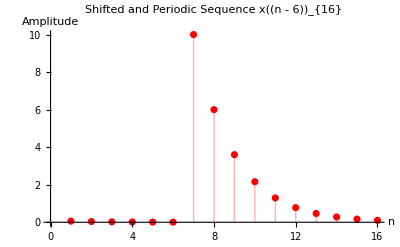

```mathematica
ListPlot[Table[10*(0.6)^Mod[n-6,16],{n,0,15}],Filling->Axis,PlotStyle->Red,AxesLabel->{"n","Amplitude"},PlotLabel->"Shifted and Periodic Sequence x((n - 6))_{16}"]
```